```mathematica
Clear["Global`*"]
DSolve[Ib*(β''[ψ]+Ω*β[ψ])==Ma,β[ψ],ψ]
```

{{β[ψ]→Ma/(Ib Ω)+C[1] Cos[ψ √Ω]+C[2] Sin[ψ √Ω]}}

1.

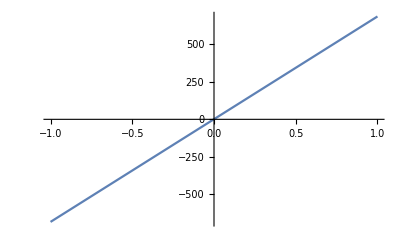

```mathematica
Clear["Global`*"]
δ[Γ_] := 1+0.1*Γ/(1.46*10^-4)
δ[0]
Plot[δ[x],{x,-1,1}]
```